```mathematica
DSolve[{y''[x]+y[x]*x^2m^4==0},y[x],x]
```

{{y[x]→C[1] ParabolicCylinderD[-1/2,(-1)^(1/4) √2 m x]+C[2] ParabolicCylinderD[-1/2,(-1)^(3/4) √2 m x]}}

```mathematica
ParabolicCylinderD[-1/2,0]
```

(√π)/(2^(1/4) Gamma[3/4])

```mathematica
ParabolicCylinderD[-1/2,0]
```

(√π)/(2^(1/4) Gamma[3/4])

```mathematica
D[ParabolicCylinderD[-1/2,x],x]
```

1/2 x ParabolicCylinderD[-1/2,x]-ParabolicCylinderD[1/2,x]

```mathematica
Sol[x_,m_]:=ParabolicCylinderD[-1/2,m(1+I)x]-ParabolicCylinder[-1/2,m(-1+I)x]
```

```mathematica
FullSimplify[D[Sol[x],x]/.{x->1}]
```

Sol'[1]

```mathematica
der[m_]:=ⅈ m (m ParabolicCylinderD[-1/2,(1+ⅈ) m]-(1-ⅈ) (ParabolicCylinderD[1/2,(1+ⅈ) m]+ⅈ Derivative[0,1][ParabolicCylinder][-1/2,(-1+ⅈ) m]))
```

```mathematica
NSolve[der[m]==0,m]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{m→0.}}

```mathematica
FindRoot[der[m]==0,{m,0.1}]
```

FindRoot::nlnum: The function value {(0.`  + 0.1` ⅈ) ((0.11581335375890106`  - 0.0058136541018157` ⅈ) - (1.`  - 1.` ⅈ) ((0.6423699994229543`  + 0.054797137183475245` ⅈ) + (0.`  + 1.` ⅈ) SuperscriptBox[ is not a list of numbers with dimensions {1} at {m} = {0.1`}.

FindRoot[der[m]==0,{m,0.1}]

```mathematica
N[FullSimplify[der[0.1]]]
```

(-0.0581759-0.0581354 ⅈ)+(0.1-0.1 ⅈ) ParabolicCylinder^(0,1)[-0.5,-0.1+0.1 ⅈ]

```mathematica
N[Derivative[0,1][ParabolicCylinder][-0.5,0.1]]
```

ParabolicCylinder^(0,1)[-0.5,0.1]

```mathematica
N[BesselJ[-1/4,1]]
```

0.669385

```mathematica
N[BesselJ[1/4,1]]
```

0.752231

```mathematica
fun1[x_]:=2^{-5/4}*Sqrt[π x]*(BesselJ[-1/4,x^2/4]+BesselJ[1/4,x^2/4])
```

```mathematica
fun2[x_]:=2^{-5/4}*Sqrt[π x]*(BesselJ[-1/4,x^2/4]-BesselJ[1/4,x^2/4])
```

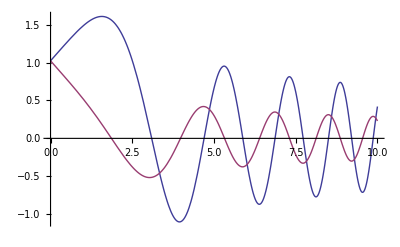

```mathematica
Plot[{fun1[x],fun2[x]},{x,0,10}]
```

```mathematica
funm1[x_]:=1/2 √π √(m x) (BesselJ[-1/4,(m^2 x^2)/2]+BesselJ[1/4,(m^2 x^2)/2])
```

```mathematica
funm2[x_]:=1/2 √π √(m x) (BesselJ[-1/4,(m^2 x^2)/2]-BesselJ[1/4,(m^2 x^2)/2])
```

```mathematica
funderm1=FullSimplify[D[funm1[x],x]]
```

1/2 m √π (m x)^(3/2) (BesselJ[-3/4,(m^2 x^2)/2]-BesselJ[3/4,(m^2 x^2)/2])

```mathematica
funderm2=FullSimplify[D[funm2[x],x]]
```

-1/2 m √π (m x)^(3/2) (BesselJ[-3/4,(m^2 x^2)/2]+BesselJ[3/4,(m^2 x^2)/2])

```mathematica
NSolve[funm1[0]*funderm2[1]-funm2[0]*funderm1[1]==0,m]
```

∞::indet: Indeterminate expression 0 √π ComplexInfinity encountered.

{{}}

```mathematica
Limit[funm1[x],x->0]
```

((m^2)^(3/4) √(π/2))/(m^(3/2) Gamma[3/4])

```mathematica
Limit[funm2[x],x->0]
```

((m^2)^(3/4) √(π/2))/(m^(3/2) Gamma[3/4])

```mathematica
FullSimplify[funderm1/.{x->1}]
```

1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]-BesselJ[3/4,m^2/2])

```mathematica
FullSimplify[funderm2/.{x->1}]
```

-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]+BesselJ[3/4,m^2/2])

```mathematica
FullSimplify[-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]+BesselJ[3/4,m^2/2])-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]-BesselJ[3/4,m^2/2])==0]
```

m^(5/2) BesselJ[-3/4,m^2/2]==0

```mathematica
BesselJZero[-3/4,10]
```

BesselJZero[-3/4,10]

```mathematica
N[BesselJZero[-3/4,1]]
```

1.05851

```mathematica
Zeros=Table[N[Sqrt[2BesselJZero[-3/4,i]],10],{i,1,100}]
```

{1.454997085,2.927133004,3.857578101,4.601777732,5.240824067,5.809787864,6.327694301,6.806248002,7.25326169,7.6742593,8.073317953,8.453548974,8.817390869,9.166797024,9.503360989,9.828402986,10.14303138,10.44818742,10.74467855,11.0332036,11.31437223,11.58872006,11.8567207,12.11879537,12.37532065,12.62663484,12.8730432,13.11482231,13.3522237,13.58547689,13.81479204,14.04036213,14.26236488,14.48096438,14.69631251,14.90855018,15.11780841,15.32420926,15.5278667,15.72888729,15.92737088,16.12341118,16.31709625,16.508509,16.69772758,16.88482577,17.06987328,17.25293611,17.43407678,17.61335459,17.79082587,17.96654416,18.14056039,18.31292309,18.48367852,18.65287083,18.82054216,18.98673282,19.15148136,19.31482468,19.47679813,19.63743561,19.79676966,19.95483148,20.11165108,20.26725729,20.42167785,20.57493946,20.72706782,20.87808772,21.02802303,21.17689679,21.32473123,21.47154783,21.61736732,21.76220974,21.90609448,22.04904029,22.1910653,22.3321871,22.47242269,22.61178856,22.7503007,22.88797461,23.02482533,23.16086744,23.29611511,23.4305821,23.56428178,23.69722713,23.82943078,23.96090501,24.09166175,24.22171263,24.35106896,24.47974174,24.60774171,24.7350793,24.86176469,24.98780781}

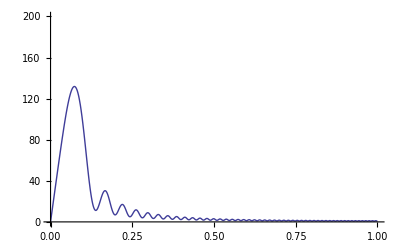

```mathematica
Plot[Sum[(funm1[x]/.{m->Zeros[[i]]})-(funm2[x]/.{m->Zeros[[i]]}),{i,1,100}],{x,0,1},PlotRange->{{0,1},{0,200}}]
```

## Testing solution

```mathematica
test=Sqrt[π x]*BesselJ[-1/4,x^2/4]
```

√π √x BesselJ[-1/4,x^2/4]

```mathematica
FullSimplify[D[test,{x,2}]]
```

-1/4 √π x^(5/2) BesselJ[-1/4,x^2/4]

```mathematica
FullSimplify[D[test,{x,2}]+x^2/4*test]
```

0

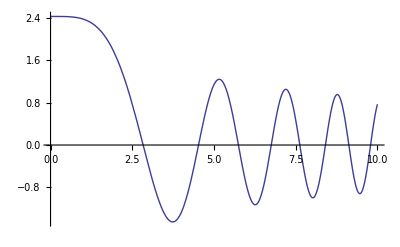

```mathematica
Plot[test,{x,0,10}]
```

```mathematica
sol1=Sqrt[m x]*BesselJ[-1/4,m^2 x^2/2]
```

√(m x) BesselJ[-1/4,(m^2 x^2)/2]

```mathematica
sol1
```

√x BesselJ[-1/3,2/3 m x^(3/2)]

```mathematica
sol2=Sqrt[m x]*BesselJ[1/4,m^2 x^2/2]
```

√(m x) BesselJ[1/4,(m^2 x^2)/2]

```mathematica
Limit[sol1,x->0]
```

(√2 (m^2)^(3/4))/(m^(3/2) Gamma[3/4])

```mathematica
Limit[sol2,x->0]
```

0

```mathematica
sol1
```

√(m x) BesselJ[-1/4,(m^2 x^2)/2]

```mathematica
dersol1=FullSimplify[D[sol1,x]]
```

-m (m x)^(3/2) BesselJ[3/4,(m^2 x^2)/2]

```mathematica
dersol2=FullSimplify[D[sol2,x]]
```

m (m x)^(3/2) BesselJ[-3/4,(m^2 x^2)/2]

```mathematica
Limit[dersol1,x->1]
```

-m^(5/2) BesselJ[3/4,m^2/2]

```mathematica
Limit[dersol2,x->1]
```

m^(5/2) BesselJ[-3/4,m^2/2]

```mathematica
Zerostrue=Table[Sqrt[2BesselJZero[-3/4,i]],{i,1,40}];
```

```mathematica
coeffs=Table[BesselJZero[-3/4,i],{i,1,200}];
```

```mathematica
Zeros=Table[N[Sqrt[2BesselJZero[-3/4,i]],10],{i,1,40}]
```

{1.454997085,2.927133004,3.857578101,4.601777732,5.240824067,5.809787864,6.327694301,6.806248002,7.25326169,7.6742593,8.073317953,8.453548974,8.817390869,9.166797024,9.503360989,9.828402986,10.14303138,10.44818742,10.74467855,11.0332036,11.31437223,11.58872006,11.8567207,12.11879537,12.37532065,12.62663484,12.8730432,13.11482231,13.3522237,13.58547689,13.81479204,14.04036213,14.26236488,14.48096438,14.69631251,14.90855018,15.11780841,15.32420926,15.5278667,15.72888729}

```mathematica
Table[N[BesselJZero[-3/4,i],10],{i,1,10}]
```

{1.058508259,4.284053813,7.440454404,10.58817915,13.73311845,16.87681751,20.01985758,23.16250593,26.30490257,29.4471279}

```mathematica
N[BesselJ[3/4,BesselJZero[-3/4,3]]]
```

0.207121

```mathematica
N[BesselJ[1/4,BesselJZero[-3/4,1]]]
```

0.742897

```mathematica
sol2
```

√(m x) BesselJ[1/4,(m^2 x^2)/2]

```mathematica
sol2m=√x BesselJ[1/4,(m^2 x^2)/2]
```

√x BesselJ[1/4,(m^2 x^2)/2]

```mathematica
Plot[Sum[(sol2m/.{m->Zerostrue[[i]]}),{i,1,10}],{x,0,1},PlotRange->{{0,1},{0,100}}]
```

$Aborted

```mathematica
NIntegrate[x^3 BesselJ[1/4,x^2/2*Zerostrue[[2]]^2]*BesselJ[1/4,x^2/2*Zerostrue[[2]]^2],{x,0,1}]
```

0.0368546

```mathematica
wmcubic=Table[NIntegrate[x^3 BesselJ[1/4,x^2/2*Zerostrue[[i]]^2]^2,{x,0,1}],{i,1,40}]
```

{0.137974,0.0368546,0.0213316,0.0150107,0.0115796,0.00942524,0.00794677,0.00686924,0.00604903,0.0054038,0.00488295,0.00445368,0.00409379,0.00378771,0.00352422,0.003295,0.00309378,0.00291572,0.00275704,0.00261474,0.00248641,0.00237009,0.00226416,0.0021673,0.00207838,0.00199648,0.00192078,0.00185062,0.0017854,0.00172462,0.00166784,0.00161468,0.00156481,0.00151792,0.00147376,0.0014321,0.00139273,0.00135547,0.00132015,0.00128662}

```mathematica
wmcubicpredefined={0.13797406599320738,0.036854581143239175,0.02133155594370827,0.015010686087355087,0.011579602879061325,0.009425240459319681,0.00794676552988761,0.006869235708429393,0.006049027438296182,0.005403797343711836,0.004882949141705082,0.0044536787382349384,0.0040937854185415555,0.0037877079495512375,0.0035242151877391964,0.003294997916730558,0.0030937766542952425,0.002915717555439377,0.0027570390413366227,0.0026147402465559653,0.0024864094328322945,0.002370086181472648,0.002264160539779118,0.0021672980550348627,0.0020783832616715044,0.0019964765310819576,0.0019207807375925753,0.001850615230525651,0.001785395309967969,0.0017246158947239064,0.0016678384163521522,0.0016146802195225812,0.0015648059267859933,0.0015179203557653368,0.0014737626725206412,0.0014321015367415484,0.0013927310476398757,0.0013554673405968029,0.00132014571598235,0.0012866182056656857}
```

{0.137974,0.0368546,0.0213316,0.0150107,0.0115796,0.00942524,0.00794677,0.00686924,0.00604903,0.0054038,0.00488295,0.00445368,0.00409379,0.00378771,0.00352422,0.003295,0.00309378,0.00291572,0.00275704,0.00261474,0.00248641,0.00237009,0.00226416,0.0021673,0.00207838,0.00199648,0.00192078,0.00185062,0.0017854,0.00172462,0.00166784,0.00161468,0.00156481,0.00151792,0.00147376,0.0014321,0.00139273,0.00135547,0.00132015,0.00128662}

```mathematica
wmfivetwo=Table[NIntegrate[x^(5/2) BesselJ[1/4,x^2/2*Zerostrue[[i]]^2],{x,0,1}],{i,1,40}]
```

{0.209965,0.0181809,0.0069193,0.00373185,0.00236737,0.00165045,0.00122407,0.000948389,0.000759097,0.000623069,0.000521773,0.000444147,0.000383242,0.000334505,0.000294845,0.000262104,0.000234734,0.000211602,0.000191861,0.000174867,0.000160124,0.000147245,0.000135921,0.000125909,0.000117008,0.000109058,0.000101925,0.0000954983,0.0000896863,0.0000844115,0.0000796084,0.0000752211,0.0000712022,0.0000675107,0.0000641113,0.0000609733,0.0000580702,0.0000553784,0.0000528777,0.00005055}

```mathematica
wmfivetwopredefined={0.20996479709362217,0.018180897590318785,0.006919303361557072,0.0037318500468507265,0.0023673658890243144,0.0016504522182779553,0.0012240656323313512,0.0009483894730813764,0.0007590968780885121,0.0006230691899630487,0.000521773141559365,0.0004441474396258039,0.00038324243624026397,0.00033450473194280715,0.0002948449039830018,0.0002621039555673866,0.0002347343932804438,0.00021160239472918784,0.00019186109713872825,0.00017486713895424112,0.00016012432055124612,0.00014724473213250115,0.0001359214046973261,0.00012590872750600792,0.00011700820222555297,0.0001090579288501799,0.00010192474302362525,0.00009549826478267914,0.00008968634379190777,0.00008441153749062422,0.00007960836196536182,0.00007522112702512196,0.00007120221729922205,0.00006751071698186362,0.0000641113016165315,0.000060973339051508034,0.00005807015547318643,0.00005537843263812609,0.00005287771007323228,0.00005054997178480274}
```

{0.209965,0.0181809,0.0069193,0.00373185,0.00236737,0.00165045,0.00122407,0.000948389,0.000759097,0.000623069,0.000521773,0.000444147,0.000383242,0.000334505,0.000294845,0.000262104,0.000234734,0.000211602,0.000191861,0.000174867,0.000160124,0.000147245,0.000135921,0.000125909,0.000117008,0.000109058,0.000101925,0.0000954983,0.0000896863,0.0000844115,0.0000796084,0.0000752211,0.0000712022,0.0000675107,0.0000641113,0.0000609733,0.0000580702,0.0000553784,0.0000528777,0.00005055}

```mathematica
coeffs=wmfivetwopredefined/wmcubicpredefined
```

{1.52177,0.493314,0.324369,0.248613,0.204443,0.17511,0.154033,0.138063,0.125491,0.115302,0.106856,0.099726,0.0936157,0.0883132,0.0836626,0.079546,0.0758731,0.072573,0.0695895,0.0668774,0.0643998,0.0621263,0.0600317,0.0580948,0.0562977,0.0546252,0.0530642,0.0516035,0.0502333,0.0489451,0.0477315,0.0465858,0.0455023,0.0444758,0.0435018,0.0425761,0.0416952,0.0408556,0.0400544,0.039289}

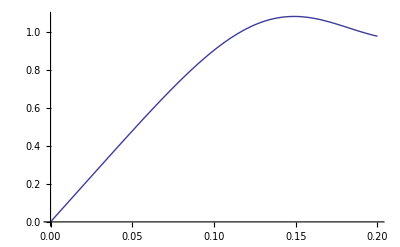

```mathematica
Plot[Sum[coeffs[[i]]Sqrt[x]*BesselJ[1/4,Zeros[[i]]^2*x^2/2],{i,1,40}],{x,0,0.2}]
```

```mathematica
N[Hypergeometric0F1[1/4,-1/4 BesselJZero[-3/4,2]^2]]
```

-2.65582×10^-15

```mathematica
Integrate[x^(5/2) BesselJ[1/4,x^2/2*Zerostrue[[2]]^2],{x,0,1}]
```

Limit::ztest1: Unable to decide whether numeric quantity Hypergeometric0F1[1/4, -1/4 BesselJZero[-3/4, 2]^2] is equal to zero. Assuming it is.

1/(2^(1/4) BesselJZero[-3/4,2]^(7/4) Gamma[1/4])

```mathematica
NIntegrate[x*BesselJ[1/4,x^2*coeffs[[1]]]*BesselJ[1/4,x^2*coeffs[[2]]],{x,0,1}]
```

0.0714686

```mathematica
N[Integrate[x*BesselJ[1/4,x^2/4]BesselJ[3/4,x^2/4],{x,0,1}]]
```

0.0371135

```mathematica
Integrate[x*BesselJ[1/4,x^2/4],{x,0,1}]
```

(4 2^(1/4) HypergeometricPFQ[{5/8},{5/4,13/8},-1/64])/(5 Gamma[1/4])

```mathematica
N[BesselJ[1/4,1]]
```

0.752231

## Linear Profile

```mathematica
DSolve[y''[x]+y[x]*x==0,y[x],x]
```

{{y[x]→AiryAi[(-1)^(1/3) x] C[1]+AiryBi[(-1)^(1/3) x] C[2]}}

```mathematica
sol1=Sqrt[x]BesselJ[-1/3,2/3m x^(3/2)]
```

√x BesselJ[-1/3,2/3 m x^(3/2)]

```mathematica
FullSimplify[D[sol1,{x,2}]+sol1*x*m^2]
```

0

```mathematica
sol2=Sqrt[x]*BesselJ[1/3,2/3*m*x^(3/2)]
```

√x BesselJ[1/3,2/3 m x^(3/2)]

```mathematica
FullSimplify[D[sol2,{x,2}]+sol2*x*m^2]
```

0

```mathematica
Limit[sol1,x->0]
```

3^(1/3)/(m^(1/3) Gamma[2/3])

```mathematica
Limit[sol2,x->0]
```

0

```mathematica
dersol1=FullSimplify[D[sol1,x]]
```

-m x BesselJ[2/3,2/3 m x^(3/2)]

```mathematica
dersol2=FullSimplify[D[sol2,x]]
```

m x BesselJ[-2/3,2/3 m x^(3/2)]

```mathematica
FullSimplify[Limit[dersol1,x->1]]
```

-(m^(5/3) Hypergeometric0F1Regularized[5/3,-m^2/9])/3^(2/3)

```mathematica
FullSimplify[Limit[dersol2,x->1]]
```

3^(2/3) m^(1/3) Hypergeometric0F1Regularized[1/3,-m^2/9]

```mathematica
Limit[dersol2,x->1]
```

1/2 m^(1/3) (-3 AiryAiPrime[-m^(2/3)]+√3 AiryBiPrime[-m^(2/3)])

```mathematica
Reduce[{Hypergeometric0F1Regularized[1/3,-m^2/9]==0,m>0},m]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{Hypergeometric0F1Regularized[1/3,-m^2/9]==0,m>0},m]

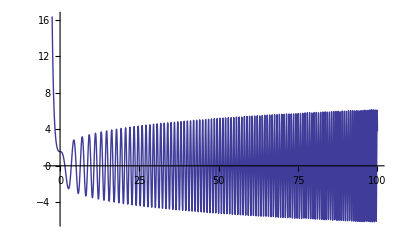

```mathematica
Plot[-3 AiryAiPrime[-x]+√3 AiryBiPrime[-x],{x,-3,100}]
```

```mathematica
Reduce[{-3 AiryAiPrime[-x]+√3 AiryBiPrime[-x]},x,Reals]
```

Reduce::naqs: And[-3 AiryAiPrime[-x] + √3 AiryBiPrime[-x]] is not a quantified system of equations and inequalities.

```mathematica
FindRoot[{-3 AiryAiPrime[-x]+√3 AiryBiPrime[-x]==0},{x,7}]
```

{x→17.4104}

```mathematica
Reduce[{Hypergeometric0F1Regularized[1/3,-m^2/9]==0,m]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Hypergeometric0F1Regularized[1/3,-m^2/9]==0,m]

```mathematica
FullSimplify[Hypergeometric0F1[1/3,x]]
```

```mathematica
FunctionExpand[Hypergeometric0F1[a,-m^2/9]]
```

3^(-1+a) m^(1-a) BesselJ[-1+a,(2 m)/3] Gamma[a]

```mathematica
N[BesselJZero[-2/3,1]]
```

1.24305

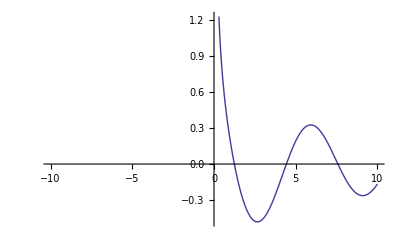

```mathematica
Plot[BesselJ[-2/3,x],{x,-10,10}]
```

```mathematica
FullSimplify[D[BesselJ[0,x^2]+2x^2BesselJ[0,x^2],{x,2}]]
```

-4 (-1+x^2+2 x^4) BesselJ[0,x^2]+2 (1-6 x^2) BesselJ[1,x^2]

```mathematica
oldtest=√x BesselJ[1/4,(m^2 x^2)/2]
```

√x BesselJ[1/4,(m^2 x^2)/2]

```mathematica
FullSimplify[D[oldtest,{x,2}]+m^4 x^2 oldtest]
```

0